## Parametri e Variabili:

```mathematica
(*Parametri Modello*)
b1 = 2;
b2 = 2;
alfa1 = 1;
alfa2 = 1;
alfa3 = 1;
sigma = 1;

(*Numero di spin = numero di popolazioni*)
Nspin=300;
(*Numero di iterazioni e passo iterativo*)
Niter=100000;
dt=0.09 ;(*così è ordine N *)


(*Niter = 20000;
dt = 0.001; *)(*così è ordine 1 *)
```

## Condizioni iniziali:

```mathematica
X=Table[RandomReal[{-1,1}],{iy,1,Nspin}];
MediaX=Table[Total[X]/Nspin, {iy,1,Niter}];
MediaX[[1]]

x1 = Table[0,{im,1,Niter}]; (* la prima diffusione *)

eps = 0.3; (* se vuoi un bias nella magnetizzazione iniziale *)
m = Table[RandomReal[{-1+eps,1}], {im, 1, Nspin}];

m1 = Table[0, {im,1,Niter}]; (* la prima magnetizzazione *)
m2 = Table[0, {im,1,Niter}]; (* la seconda magnetizzazione *)

M = Table[Total[m]/Nspin,{iy,1,Niter}]; (* la magnetizzazione totale *)

M[[1]]

(* vorremmo inserire anche un dato non zero, almeno per la M *)
```

0.0369224

0.103928

## Simulazioni Sistema Stocastico:

```mathematica
For[i=1,i≤Niter-1, i++,
M[[i]]=Total[m]/Nspin;
m1[[i]] = m[[1]];
m2[[i]] = m[[2]];
MediaX[[i]] = Total[X]/Nspin;
x1[[i]] = X[[1]];

U1 = RandomVariate[UniformDistribution[],Nspin];
U2 = RandomVariate[UniformDistribution[],Nspin];
Noise=RandomVariate[NormalDistribution[],Nspin];

W1=Boole[Table[Nspin*(1 + m[[j]])/2*Exp[-b1*m[[j]] (*- b2*M[[i]]*) - b1*X[[j]] (*- b2*MediaX[[i]]*)]*dt>U1[[j]],{j,1,Nspin}]];
W2=Boole[Table[Nspin*(1 - m[[j]])/2*Exp[b1*m[[j]] (*+ b2*M[[i]]*) + b1*X[[j]] (*+ b2*MediaX[[i]]*)]*dt>U2[[j]],{j,1,Nspin}]];


X = X - alfa2/Nspin*(X - MediaX[[i]])*dt  - alfa3/(Nspin)^2*MediaX[[i]] *dt + sigma/(Sqrt[Nspin])*Noise *dt^(1/2);

m = m - W1*(2/Nspin) + W2*(2/Nspin);
];
```

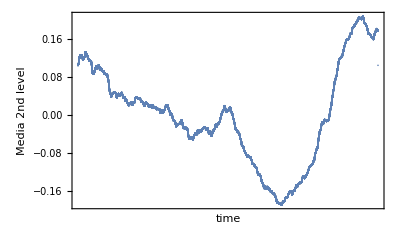

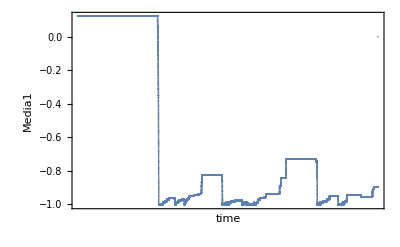

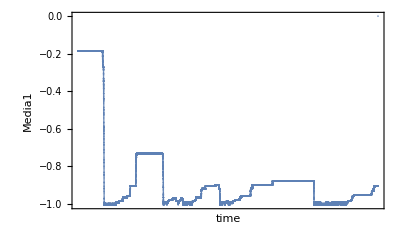

```mathematica
A=ListPlot[M,Frame->True,Axes->False,FrameLabel->{"time","Media 2nd level"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]

B =ListPlot[m1,Frame->True,Axes->False,FrameLabel->{"time","Media1"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]

L = ListPlot[m2,Frame->True,Axes->False,FrameLabel->{"time","Media1"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```

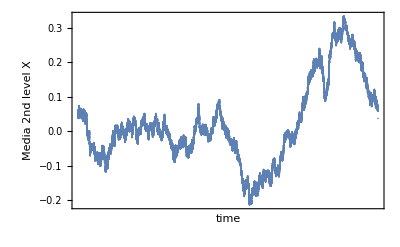

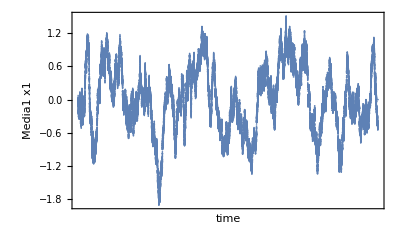

```mathematica
H=ListPlot[MediaX,Frame->True,Axes->False,FrameLabel->{"time","Media 2nd level X"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]

G =ListPlot[x1,Frame->True,Axes->False,FrameLabel->{"time","Media1 x1"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```